```mathematica
data = Import[NotebookDirectory[]<>"dupless_data_500.wxf"];
```

```mathematica
Export[NotebookDirectory[]<> "dataTrain.wxf", dataTrain];
Export[NotebookDirectory[]<> "dataValidate.wxf", dataValidate];
Export[NotebookDirectory[]<> "dataTest.wxf", dataTest];
```

```mathematica
dataTrain = RandomSample[Import[NotebookDirectory[]<> "dataTrain.wxf"]];
dataValidate = RandomSample[Import[NotebookDirectory[]<> "dataValidate.wxf"]];
dataTest = Import[NotebookDirectory[]<> "dataTest.wxf"];
```

```mathematica
dataTrain[[;;1]]
```

{{48,227,141,177,125,144,136,177,39,46,51,54,188,142,53,188,141,177,54,229,56,178,142,187,144,177,58,188,134,177,127,146,177,36,39,56,227,144,177,54,227,142,177,127,124,139,177,32,48,44,54,184,142,177,53,184,141,177,54,184,142,177,53,201,132,177,141,177,51,42,227,136,177,120,139,130,177,34,41,49,46,253,137,177,51,189,139,177,53,188,129,177,122,141,177,31,34,51,227,139,177,49,227,137,122,119,134,177,27,43,39,48,202,136,177,49,202,137,177,48,202,136,177,49,201,127,131,177,115,137,177,32,44,39,49,189,120,177,20,180,137,177,48,184,108,177,22,180,136,49,185,110,177,24,179,137,48,186,112,177,25,189,113,177,27,189,115,177,29,189,117,177,30,189,118,177,32,189,120,177,34,189,122,177,36,189,124,177,37,183,136,182,132,127,125,177,39,46,189,127,177,41,189,129,177,42,189,130,177,41,189,129,134,177,39,44,189,127,177,37,189,125,177,36,189,124,177,34,189,122,177,32,189,120,177,30,189,118,177,29,189,117,177,27,188,132,177,115,177,53,25,187,141,177,51,187,139,177,53,232,141,177,54,189,142,177,56,189,144,177,54,227,142,177,53,227,141,113,177,53,184,141,177,51,184,139,177,53,184,141,177,51,202,139,177,49,227,137,177,59,56,49,29,227,144,147,177,54,58,202,117,177,30,189,118,177,32,188,137,177,146,142,120,177,58,49,54,30,227,118,177,29,227,117,142,146,177,56,59,29,189,117,177,27,189,115,177,29,189,117,177,27,189,115,177,25,229,147,144,177,137,177,113,177,37,54,58,227,125,177,36,202,146,177,59,189,147,177,61,188,142,177,149,124,177,37,59,227,147,177,58,227,146,177,58,184,146,177,56,184,144,177,58,184,146,177,56,202,144,177,54,227,142,125,177,24,56,54,63,227,151,142,177,61,53,202,112,177,25,189,113,177,27,189,115,141,149,177,25,61,53,227,113,177,24,227,112,141,149,177,24,63,54,189,112,177,22,189,110,177,24,189,112,177,22,189,110,177,20,228,144,177,108,178,28,226,151,178,116,177,60,27,200,56,177,142,190,144,57,190,148,177,115,177,145,177,61,56,28,228}}

```mathematica
dataTrain100= Partition[#, 100]&/@ dataTrain;
```

```mathematica
dataValidate100= Partition[#, 100]&/@ dataValidate;
```

```mathematica
dataValidate100 = Flatten[dataValidate100,1];
```

```mathematica
dataTrain100//Dimensions
```

{421960,100}

```mathematica
dataValidate100//Dimensions
```

{49645,100}

```mathematica
Import[NotebookDirectory[]<> "dataTrain.wxf"]//Dimensions
```

{84392,500}

```mathematica
Export[NotebookDirectory[]<> "dataTrain100.wxf", dataTrain100];
Export[NotebookDirectory[]<> "dataValidate100.wxf", dataValidate100];
```

```mathematica
{dataTrain,dataValidate,dataTest} =TakeList[shuffledData,{Round[0.85*Length[shuffledData]],Round[0.1*Length[shuffledData]],All}];
```

$Aborted[]

```mathematica
{dataTrain,dataValidate,dataTest}=With[{fullData=RandomSample[data]},
TakeList[fullData,{Round[0.85*Length[fullData]],Round[0.1*Length[fullData]],All}]
];
```

Intersection sanity check

```mathematica
Intersection[dataTrain, dataValidate]
Intersection[dataTrain, dataTest]
Intersection[dataTest, dataValidate]
```

{}

{}

{}

```mathematica
predict = NetChain[{
UnitVectorLayer[310],
GatedRecurrentLayer[512],
GatedRecurrentLayer[512],
NetMapOperator[LinearLayer[310]],
SoftmaxLayer[]
}
]
```

NetChain[<>]

```mathematica
dataTrain//Dimensions
```

{84392,500}

```mathematica
teacherForcingNet=NetGraph[<|"predict"->predict,"rest"->SequenceRestLayer[],"most"->SequenceMostLayer[],"loss"->CrossEntropyLossLayer["Index"]|>,{NetPort["Input"]->"most"->"predict"->NetPort["loss","Input"],NetPort["Input"]->"rest"->NetPort["loss","Target"]},"Input"-> {500,"Integer"}]
```

NetGraph[<>]

```mathematica
result=NetTrain[teacherForcingNet,<|"Input"->dataTrain[[;;10]] |>,All,BatchSize->64 , TargetDevice->"GPU", ValidationSet-> <|"Input"->dataValidate [[;;10]]|>]
```

NetTrainResultsObject[<>]

```mathematica
result["TrainedNet"]
```

NetGraph[<>]

```mathematica
Export["testnet.wlnet",result]
```

Export::invnet2: The second argument in Export[C:\Users\leo\Documents\testnet.wlnet,result] is not a valid net.

$Failed

```mathematica
trained=NetExtract[trainedNet,"predict"]
```

NetChain[<>]

```mathematica
predictNet=NetJoin[NetTake[trained,3,"Input"->Automatic],{SequenceLastLayer[],NetExtract[trained,{4,"Net"}],SoftmaxLayer[]},"Input"->"Varying","Output"->NetDecoder[{"Class",Range[310]}]]
```

NetChain[<>]

```mathematica
tempNet = NetTake[predictNet, 5]
```

NetChain[<>]

```mathematica
sampler = NetTake[predictNet, -1];
```

```mathematica
predictNet[{},"TopProbabilities"]
```

NetChain::netemptin: Empty inputs are not permitted.

$Failed

```mathematica
results =First@Import[NotebookDirectory[]<> "perfomance_rnn_final_all.mx"];
```

```mathematica
Keys[results]
```

{BatchErrorRateList,BatchLossList,BatchSize,CheckpointingFiles,CompactErrorRateEvolutionPlot,CompactLossEvolutionPlot,ErrorRateEvolutionPlot,EvolutionPlots,FinalLearningRate,FinalRoundErrorRate,FinalRoundLoss,FinalValidationErrorRate,FinalValidationLoss,InitialLearningRate,LossEvolutionPlot,LowestValidationErrorRate,LowestValidationLoss,LowestValidationRound,MeanBatchesPerSecond,MeanInputsPerSecond,NetTrainInputForm,OptimizationMethod,RoundErrorRateList,RoundLossList,TotalBatches,TotalInputs,TotalRounds,TotalTrainingTime,TrainedNet,TrainingNet,ValidationErrorRateList,ValidationErrorRateSeries,ValidationLossList,ValidationLossSeries,VersionNumber,WeightsLearningRateMultipliers,Properties}

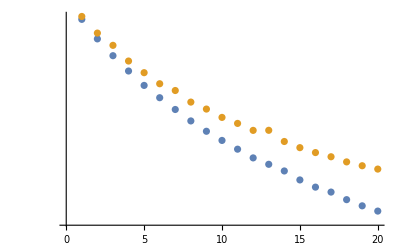

```mathematica
ListLogPlot[{results["RoundLossList"],results["ValidationLossList"][[All,2]]}]
```

1.43

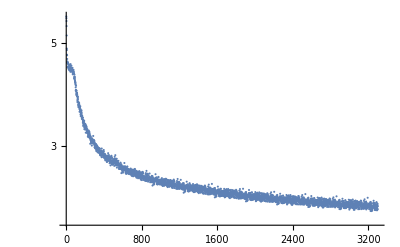

```mathematica
143/1000.*10
```

```mathematica
trainedNet =Import[NotebookDirectory[]<> "perfomance_rnn_final_v1.wlnet"]
```

NetGraph[<>]

```mathematica
testNet=NetTake[trainedNet,{"predict","predict"},"Output"->NetDecoder[{"Class",Range[310]}]]
```

NetGraph[<>]

```mathematica
testNet@Most@dataTest[[1]]
```

{178,178,178,178,178,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177,177}

```mathematica
Count[MapThread[SameQ,{%341,Rest@dataTest[[1]]}],True]
%341-Rest
```

92

```mathematica
ClassifierMeasurements[trained, dataTest, "Accuracy"];
```

ClassifierMeasurements::mlcntclnet: This neural network cannot be converted to a ClassifierFunction[…].

```mathematica
predictNet[{2}, "RandomSample"]
```

165

```mathematica
generateSample[net_, start_,len_,temp_: 1]:=With[{obj=NetStateObject[net]},Join@NestList[{sampler[obj[#]/temp,"RandomSample"]}&,{start},len]]
```

```mathematica
generateSample[net_,start_,len_]:=Block[{obj=NetStateObject[net]},Join@NestList[{obj[#,"RandomSample"]}&,{start},len]]
```

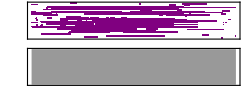

```mathematica
generated = Flatten[generateSample[tempNet, 88+88+1, 1000, 1.1219]]; 
Sound[toSound[oneHotEncoding/@generated]]// Quiet
```

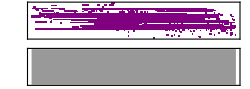

```mathematica
generated = Flatten[generateSample[predictNet, 88+88+1, 2000]];
Sound[toSound[oneHotEncoding/@generated]] // Quiet
```

```mathematica
Export[NotebookDirectory[]<>"gen_something.wxf", generated]
```

C:\Users\leo\Desktop\WSS\WSS18\Project\gen_something.wxf

```mathematica
EmitSound[%368]
```

```mathematica
Export[NotebookDirectory[]<>"gen4.wxf", %414]
```

C:\Users\leo\Desktop\WSS\WSS18\Project\gen4.wxf

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

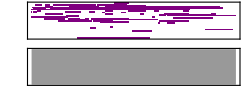

```mathematica
Import[NotebookDirectory[]<> "gen4.wxf"]
```

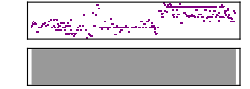

```mathematica
Sound[toSound[oneHotEncoding/@ Import[NotebookDirectory[]<> "gen8.wxf"]]] // Quiet
```

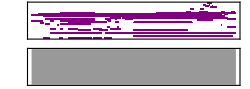

```mathematica
Sound[]
```

```mathematica
toSound[oneHotEncoding/@ Import[NotebookDirectory[]<> "gen5.wxf"]]
```

Part::take: Cannot take positions 359 through 340 in {TimeShift→0.12,NoteOff→73,NoteOff→80,NoteOff→68,TimeShift→0.01,NoteOff→61,NoteOff→75,VelocityChange→89,NoteOn→75,TimeShift→0.01,NoteOn→72,NoteOn→75,NoteOn→66,TimeShift→0.01,NoteOn→78,TimeShift→0.17,NoteOff→78,VelocityChange→82,NoteOn→77,TimeShift→0.25,NoteOff→75,VelocityChange→100,«7»,NoteOn→84,TimeShift→0.25,NoteOff→78,NoteOff→84,NoteOff→72,TimeShift→0.01,NoteOff→85,NoteOff→66,VelocityChange→104,NoteOn→68,TimeShift→0.01,VelocityChange→70,NoteOn→80,TimeShift→0.25,NoteOff→80,NoteOn→78,TimeShift→0.23,NoteOff→78,NoteOn→77,TimeShift→0.25,NoteOff→77,«351»}.

Part::take: Cannot take positions 133 through 94 in {TimeShift→0.12,NoteOff→73,NoteOff→80,NoteOff→68,TimeShift→0.01,NoteOff→61,NoteOff→75,VelocityChange→89,NoteOn→75,TimeShift→0.01,NoteOn→72,NoteOn→75,NoteOn→66,TimeShift→0.01,NoteOn→78,TimeShift→0.17,NoteOff→78,VelocityChange→82,NoteOn→77,TimeShift→0.25,NoteOff→75,VelocityChange→100,«7»,NoteOn→84,TimeShift→0.25,NoteOff→78,NoteOff→84,NoteOff→72,TimeShift→0.01,NoteOff→85,NoteOff→66,VelocityChange→104,NoteOn→68,TimeShift→0.01,VelocityChange→70,NoteOn→80,TimeShift→0.25,NoteOff→80,NoteOn→78,TimeShift→0.23,NoteOff→78,NoteOn→77,TimeShift→0.25,NoteOff→77,«351»}.

{SoundNote[D#5,{0.13,0.57},SoundVolume→89],SoundNote[C5,{0.14,8.44},SoundVolume→89],SoundNote[D#5,{0.14,2.52},SoundVolume→89],SoundNote[F#4,{0.14,3.77},SoundVolume→89],SoundNote[F#5,{0.15,1.31},SoundVolume→89],SoundNote[F5,{0.32,1.06},SoundVolume→82],SoundNote[A#5,{0.57,0.82},SoundVolume→100],SoundNote[F#5,{0.82,1.81},SoundVolume→100],SoundNote[C6,{1.06,1.31},SoundVolume→89],SoundNote[G#4,{1.32,2.32},SoundVolume→104],SoundNote[G#5,{1.33,1.58},SoundVolume→70],SoundNote[F#5,{1.58,2.52},SoundVolume→70],SoundNote[F5,{1.81,2.06},SoundVolume→70],SoundNote[G#5,{2.06,2.31},SoundVolume→70],SoundNote[D#4,{2.32,3.79},SoundVolume→82],SoundNote[G#4,{2.32,2.52},SoundVolume→82],SoundNote[D#5,{2.33,2.98},SoundVolume→82],SoundNote[F#5,{2.33,2.53},SoundVolume→100],SoundNote[C#4,{2.53,14.46},SoundVolume→82],SoundNote[G#4,{2.53,6.9},SoundVolume→82],SoundNote[C#5,{2.54,2.78},SoundVolume→85],SoundNote[F5,{2.54,2.78},SoundVolume→89],SoundNote[D#5,{2.81,3.65},SoundVolume→78],SoundNote[F#5,{2.81,3.47},SoundVolume→78],SoundNote[F5,{3.11,3.24},SoundVolume→78],SoundNote[G#5,{3.3,4.6},SoundVolume→78],SoundNote[D#5,{3.41,8.44},SoundVolume→89],SoundNote[F5,{3.48,3.77},SoundVolume→89],SoundNote[F5,{3.65,3.77},SoundVolume→89],SoundNote[C#5,{3.78,7.68},SoundVolume→89],SoundNote[F#5,{3.78,4.12},SoundVolume→85],SoundNote[F#3,{3.79,4.35},SoundVolume→78],SoundNote[G#5,{4.36,5.94},SoundVolume→93],SoundNote[C#6,{4.6,4.6},SoundVolume→82],SoundNote[C#3,{4.64,5.97},SoundVolume→82],SoundNote[F5,{4.64,5.94},SoundVolume→78],SoundNote[F5,{5.11,5.94},SoundVolume→85],SoundNote[G#2,{5.95,9.12},SoundVolume→82],SoundNote[G#3,{5.95,9.1},SoundVolume→82],SoundNote[G#4,{5.95,13.29},SoundVolume→85],SoundNote[C#2,{5.96,11.19},SoundVolume→74],SoundNote[C#3,{5.97,11.19},SoundVolume→85],SoundNote[A4,{7.4,8.44},SoundVolume→74],SoundNote[C#5,{7.4,13.29},SoundVolume→104],SoundNote[D#3,{7.4,7.55},SoundVolume→82],SoundNote[F#2,{7.4,7.67},SoundVolume→85],SoundNote[F#4,{7.4,7.69},SoundVolume→74],SoundNote[F#5,{7.4,7.68},SoundVolume→97],SoundNote[B4,{7.69,8.11},SoundVolume→85],SoundNote[B3,{7.7,8.11},SoundVolume→89],SoundNote[D5,{7.7,7.95},SoundVolume→93],SoundNote[A4,{8.11,13.43},SoundVolume→85],SoundNote[C5,{8.12,9.08},SoundVolume→85],SoundNote[F#2,{8.12,8.24},SoundVolume→67],SoundNote[B4,{8.45,8.7},SoundVolume→89],SoundNote[D#4,{8.45,9.09},SoundVolume→93],SoundNote[F#4,{8.45,9.08},SoundVolume→89],SoundNote[B3,{8.46,9.09},SoundVolume→93],SoundNote[G#3,{8.46,9.12},SoundVolume→78],SoundNote[C5,{8.7,12.24},SoundVolume→82],SoundNote[G#3,{9.09,12.23},SoundVolume→82],SoundNote[A#3,{9.1,9.94},SoundVolume→89],SoundNote[C#1,{9.12,11.19},SoundVolume→74],SoundNote[C#2,{9.13,13.27},SoundVolume→63],SoundNote[C#3,{9.13,12.22},SoundVolume→63],SoundNote[G#3,{9.94,13.27},SoundVolume→67],SoundNote[C#3,{11.2,13.28},SoundVolume→85],SoundNote[G#2,{11.2,13.29},SoundVolume→67],SoundNote[C#3,{11.21,13.44},SoundVolume→52],SoundNote[D#4,{11.21,12.23},SoundVolume→89],SoundNote[G#3,{11.21,13.3},SoundVolume→52],SoundNote[F3,{11.22,13.71},SoundVolume→59],SoundNote[F#4,{11.22,12.23},SoundVolume→70],SoundNote[C#5,{12.24,14.45},SoundVolume→67],SoundNote[F4,{12.25,13.28},SoundVolume→70],SoundNote[F5,{12.25,13.27},SoundVolume→67],SoundNote[G#3,{12.25,13.7},SoundVolume→70],SoundNote[C#2,{12.26,13.28},SoundVolume→70],SoundNote[F#4,{12.26,13.41},SoundVolume→63],SoundNote[A3,{13.31,14.47},SoundVolume→70],SoundNote[F4,{13.41,14.45},SoundVolume→59],SoundNote[G#4,{13.41,13.69},SoundVolume→59],SoundNote[F3,{13.42,13.71},SoundVolume→59],SoundNote[G#3,{13.42,14.03},SoundVolume→59],SoundNote[G#4,{13.43,13.7},SoundVolume→67],SoundNote[F1,{13.44,14.03},SoundVolume→70],SoundNote[A4,{13.69,14.02},SoundVolume→74],SoundNote[A4,{13.69,14.02},SoundVolume→93],SoundNote[C#2,{13.7,13.7},SoundVolume→70],SoundNote[G#4,{14.02,14.45},SoundVolume→52]}

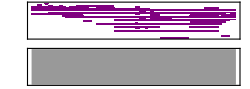

```mathematica
Sound[]
```

```mathematica
toSound[oneHotEncoding/@ Import[NotebookDirectory[]<> "gen8.wxf"]]
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

{SoundNote[A4,{0.02,0.08},SoundVolume→Last[{}]],SoundNote[B4,{0.08,0.15},SoundVolume→Last[{}]],SoundNote[D5,{0.15,0.23},SoundVolume→Last[{}]],SoundNote[C#5,{0.23,0.31},SoundVolume→Last[{}]],SoundNote[E5,{0.31,0.42},SoundVolume→Last[{}]],SoundNote[C#5,{0.42,0.5},SoundVolume→Last[{}]],SoundNote[D5,{0.5,0.62},SoundVolume→Last[{}]],SoundNote[C#5,{0.62,0.87},SoundVolume→Last[{}]],SoundNote[E4,{0.87,1.12},SoundVolume→Last[{}]],SoundNote[A4,{1.12,1.37},SoundVolume→Last[{}]],SoundNote[A4,{1.37,1.62},SoundVolume→Last[{}]],SoundNote[B4,{1.62,1.87},SoundVolume→Last[{}]],SoundNote[C#5,{1.87,2.12},SoundVolume→Last[{}]],SoundNote[D5,{2.12,2.37},SoundVolume→Last[{}]],SoundNote[B4,{2.37,2.62},SoundVolume→Last[{}]],SoundNote[C5,{2.62,2.87},SoundVolume→Last[{}]],SoundNote[E5,{2.87,3.12},SoundVolume→Last[{}]],SoundNote[F#5,{3.12,3.37},SoundVolume→Last[{}]],SoundNote[A4,{3.37,3.62},SoundVolume→Last[{}]],SoundNote[B4,{3.62,3.87},SoundVolume→Last[{}]],SoundNote[F#5,{3.62,3.87},SoundVolume→Last[{}]],SoundNote[A4,{3.87,4.12},SoundVolume→Last[{}]],SoundNote[F#4,{4.12,4.37},SoundVolume→Last[{}]],SoundNote[F#5,{4.12,4.37},SoundVolume→Last[{}]],SoundNote[A4,{4.37,4.62},SoundVolume→Last[{}]],SoundNote[C#5,{4.37,4.62},SoundVolume→Last[{}]],SoundNote[B4,{4.62,4.87},SoundVolume→Last[{}]],SoundNote[F#4,{4.62,4.87},SoundVolume→Last[{}]],SoundNote[D5,{4.87,4.99},SoundVolume→Last[{}]],SoundNote[F#4,{4.87,4.99},SoundVolume→Last[{}]],SoundNote[A4,{5.24,5.49},SoundVolume→Last[{}]],SoundNote[D5,{5.24,5.49},SoundVolume→Last[{}]],SoundNote[A4,{5.49,5.74},SoundVolume→Last[{}]],SoundNote[F#4,{5.49,5.74},SoundVolume→Last[{}]],SoundNote[B4,{5.74,6.},SoundVolume→Last[{}]],SoundNote[D4,{5.74,6.},SoundVolume→Last[{}]],SoundNote[C#4,{6.,6.25},SoundVolume→Last[{}]],SoundNote[D5,{6.,6.25},SoundVolume→Last[{}]],SoundNote[B4,{6.25,6.5},SoundVolume→Last[{}]],SoundNote[D4,{6.25,6.5},SoundVolume→Last[{}]],SoundNote[F#4,{6.5,6.75},SoundVolume→Last[{}]],SoundNote[F#5,{6.5,6.75},SoundVolume→Last[{}]],SoundNote[D4,{6.75,7.},SoundVolume→Last[{}]],SoundNote[B3,{7.,7.25},SoundVolume→Last[{}]],SoundNote[D4,{7.25,7.5},SoundVolume→Last[{}]],SoundNote[F#4,{7.5,8.},SoundVolume→Last[{}]],SoundNote[A4,{7.75,8.},SoundVolume→Last[{}]],SoundNote[B4,{8.,8.25},SoundVolume→Last[{}]],SoundNote[F#4,{8.25,8.5},SoundVolume→Last[{}]],SoundNote[B4,{8.5,8.75},SoundVolume→Last[{}]],SoundNote[B5,{8.75,9.},SoundVolume→Last[{}]],SoundNote[F#4,{9.,9.25},SoundVolume→Last[{}]],SoundNote[A3,{9.25,9.5},SoundVolume→Last[{}]],SoundNote[D4,{9.5,9.75},SoundVolume→Last[{}]],SoundNote[C4,{9.75,10.},SoundVolume→Last[{}]],SoundNote[B3,{10.,10.25},SoundVolume→Last[{}]],SoundNote[D6,{10.25,10.5},SoundVolume→Last[{}]],SoundNote[B4,{10.5,10.75},SoundVolume→Last[{}]],SoundNote[B5,{10.75,11.},SoundVolume→Last[{}]],SoundNote[B6,{11.,11.25},SoundVolume→Last[{}]],SoundNote[G6,{11.25,11.5},SoundVolume→Last[{}]],SoundNote[A4,{11.5,11.75},SoundVolume→Last[{}]],SoundNote[G4,{11.75,12.},SoundVolume→Last[{}]],SoundNote[A4,{12.,12.25},SoundVolume→Last[{}]],SoundNote[E5,{12.25,12.5},SoundVolume→Last[{}]],SoundNote[A4,{12.51,12.76},SoundVolume→Last[{}]],SoundNote[G4,{12.76,13.01},SoundVolume→Last[{}]],SoundNote[A4,{13.01,13.26},SoundVolume→Last[{}]],SoundNote[G5,{13.26,13.51},SoundVolume→Last[{}]],SoundNote[C#5,{13.51,13.76},SoundVolume→Last[{}]],SoundNote[A4,{13.76,14.01},SoundVolume→Last[{}]],SoundNote[A4,{14.01,14.26},SoundVolume→Last[{}]],SoundNote[C#4,{14.01,14.26},SoundVolume→Last[{}]],SoundNote[B4,{14.26,14.51},SoundVolume→Last[{}]],SoundNote[A4,{14.51,14.76},SoundVolume→Last[{}]],SoundNote[E4,{14.77,15.02},SoundVolume→Last[{}]],SoundNote[A4,{15.02,15.27},SoundVolume→Last[{}]],SoundNote[F#4,{15.02,15.27},SoundVolume→Last[{}]],SoundNote[A4,{15.52,15.77},SoundVolume→Last[{}]],SoundNote[B4,{15.77,16.02},SoundVolume→Last[{}]],SoundNote[A4,{16.02,16.27},SoundVolume→Last[{}]],SoundNote[E4,{16.27,16.52},SoundVolume→Last[{}]],SoundNote[A4,{16.77,17.02},SoundVolume→Last[{}]],SoundNote[A4,{17.21,17.46},SoundVolume→Last[{}]],SoundNote[A#4,{17.46,17.71},SoundVolume→Last[{}]],SoundNote[A4,{17.96,18.12},SoundVolume→Last[{}]],SoundNote[A4,{18.12,18.37},SoundVolume→Last[{}]],SoundNote[E5,{18.37,18.62},SoundVolume→Last[{}]],SoundNote[A4,{18.62,18.87},SoundVolume→127],SoundNote[C#5,{18.87,19.12},SoundVolume→127],SoundNote[A4,{19.12,19.37},SoundVolume→127],SoundNote[E5,{19.37,19.62},SoundVolume→127],SoundNote[F#5,{19.62,19.87},SoundVolume→127],SoundNote[A4,{19.87,20.12},SoundVolume→127],SoundNote[B4,{20.12,20.62},SoundVolume→108],SoundNote[D5,{20.12,20.37},SoundVolume→108],SoundNote[A4,{20.37,20.62},SoundVolume→108],SoundNote[A4,{20.62,20.87},SoundVolume→108],SoundNote[E4,{20.62,20.87},SoundVolume→108],SoundNote[G4,{20.62,20.87},SoundVolume→108],SoundNote[D4,{20.87,21.12},SoundVolume→108],SoundNote[A4,{21.12,21.37},SoundVolume→108],SoundNote[E6,{21.37,21.62},SoundVolume→108],SoundNote[E6,{21.62,21.87},SoundVolume→108],SoundNote[A5,{21.87,22.12},SoundVolume→108],SoundNote[C#6,{21.87,22.12},SoundVolume→108],SoundNote[C#7,{22.12,22.37},SoundVolume→108],SoundNote[B6,{22.37,22.62},SoundVolume→108],SoundNote[E6,{22.37,22.62},SoundVolume→108],SoundNote[A6,{22.62,23.37},SoundVolume→108],SoundNote[D#6,{22.62,22.87},SoundVolume→108],SoundNote[B6,{22.87,23.12},SoundVolume→108],SoundNote[A6,{23.12,23.62},SoundVolume→108],SoundNote[C7,{23.12,23.37},SoundVolume→108],SoundNote[A6,{23.37,31.12},SoundVolume→108],SoundNote[B6,{23.37,23.62},SoundVolume→108],SoundNote[B5,{23.62,23.87},SoundVolume→108],SoundNote[F6,{23.62,23.87},SoundVolume→108],SoundNote[A5,{23.87,24.12},SoundVolume→108],SoundNote[C6,{23.87,24.12},SoundVolume→108],SoundNote[A5,{24.37,24.62},SoundVolume→108],SoundNote[F6,{24.37,24.62},SoundVolume→108],SoundNote[C6,{24.62,24.87},SoundVolume→108],SoundNote[C7,{24.87,25.12},SoundVolume→108],SoundNote[D5,{25.12,25.37},SoundVolume→108],SoundNote[D6,{25.62,25.87},SoundVolume→108],SoundNote[C6,{25.87,26.12},SoundVolume→108],SoundNote[A#5,{26.12,26.37},SoundVolume→108],SoundNote[A5,{26.37,26.62},SoundVolume→108],SoundNote[A#5,{26.62,26.87},SoundVolume→108],SoundNote[C6,{26.87,27.12},SoundVolume→108],SoundNote[A#5,{27.12,27.37},SoundVolume→108],SoundNote[A5,{27.37,27.62},SoundVolume→108],SoundNote[F6,{27.62,27.87},SoundVolume→108],SoundNote[A5,{27.87,28.12},SoundVolume→108],SoundNote[C6,{28.12,28.37},SoundVolume→108],SoundNote[C6,{28.37,28.62},SoundVolume→108],SoundNote[A5,{28.62,28.87},SoundVolume→108],SoundNote[F5,{28.87,29.12},SoundVolume→108],SoundNote[F6,{29.12,29.37},SoundVolume→108],SoundNote[G#5,{29.37,29.62},SoundVolume→108],SoundNote[A5,{29.62,29.87},SoundVolume→108],SoundNote[E5,{29.87,30.12},SoundVolume→108],SoundNote[E6,{29.87,30.12},SoundVolume→108],SoundNote[A5,{30.12,30.37},SoundVolume→108],SoundNote[C6,{30.37,30.62},SoundVolume→108],SoundNote[E6,{30.62,30.87},SoundVolume→108],SoundNote[A5,{30.87,31.12},SoundVolume→108],SoundNote[B5,{31.12,31.37},SoundVolume→108],SoundNote[D6,{31.37,31.62},SoundVolume→108],SoundNote[F5,{31.37,31.62},SoundVolume→108],SoundNote[A5,{31.62,31.87},SoundVolume→108],SoundNote[A6,{31.62,31.87},SoundVolume→108],SoundNote[B6,{31.87,32.12},SoundVolume→108],SoundNote[A5,{32.12,32.37},SoundVolume→108],SoundNote[A6,{32.12,32.37},SoundVolume→108],SoundNote[D6,{32.37,32.62},SoundVolume→108],SoundNote[E6,{32.37,32.62},SoundVolume→108],SoundNote[B5,{32.62,32.87},SoundVolume→108],SoundNote[E6,{32.62,32.87},SoundVolume→108],SoundNote[A5,{32.87,33.12},SoundVolume→108],SoundNote[F#6,{32.87,33.12},SoundVolume→108],SoundNote[F6,{32.87,33.12},SoundVolume→108],SoundNote[B5,{33.12,33.37},SoundVolume→108],SoundNote[G#5,{33.12,33.37},SoundVolume→108],SoundNote[E5,{33.37,33.62},SoundVolume→108],SoundNote[G#5,{33.37,33.62},SoundVolume→108],SoundNote[E5,{33.62,33.87},SoundVolume→108],SoundNote[G5,{33.62,33.87},SoundVolume→108],SoundNote[E5,{33.87,34.12},SoundVolume→108],SoundNote[E6,{33.87,34.12},SoundVolume→108],SoundNote[D6,{34.12,34.37},SoundVolume→108]}

```mathematica
Sound[]
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

-Graphics-